λ = 0.65

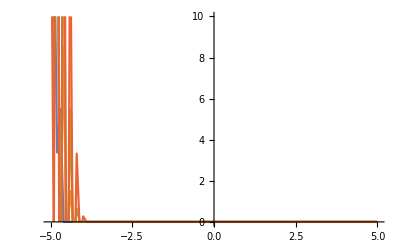

-Graphics-

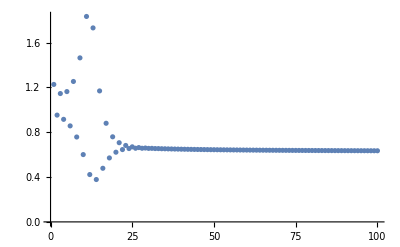

```mathematica
(*Problem #1, #2, #3*)
(* For problem #2, replace α =.55 with α = 5 *)
(* For problem #3, replace α = 2 and Δt = .001 *)

α=.5; (* IN ORDER TO SEE PLOT FOR λ = .35, .4, .45, .5, .55 JUST SET α = TO DESIRED λ and shift-enter*)
Δx=.1;
Δt=.01;
λ = α Δt/Δx^2;
Print["λ = ", α Δt/Δx^2];
(*Vector u initialization*)
u={};
x = {};
For[i=-5, i≤5,i+=Δx,
(*u(Subscript[x, i],0) = 0*)
AppendTo[u,0];
AppendTo[x,i];
];
(*u(-5,0) = 20 *)
(*u(5,0) = 0 *)
u[[1]]=20;

(*Constructing Matrix*)
A = IdentityMatrix[Length[u]];

For[i=2,i≤Length[u]-1,i++,
A[[i,i]] = 1-2λ;
A[[i,i-1]]=λ;
A[[i,i+1]]=λ;
];

(*Constructing the discrete fourier transform matrix*)
M = Length[u];
dftm = {};
(* from 0 to M - 1 (in this case 100, depends on Δx *)
For[k =0, k ≤ M -1, ++k, 
(* make a new basis vector for each frequency *)
row = {};
For[i =0, i ≤ M-1, ++i,
 (* for a given frequency k, at each ith location compute the component of that basis vector *)
xi = 2*Pi/M * i;
AppendTo[row, E^(I*k*xi)];

];

AppendTo[dftm,row];
];

dftm = dftm/Sqrt[M];

ulist = {};
clist = {};

For[t=0.0,t≤1,t+=Δt,
If[(t==.03||t==.06||t==.08||t==.1),
AppendTo[ulist,u];
];
u=A.u;
c = N[Simplify[dftm.u]];
AppendTo[clist,Abs[c[[20]]]]; (*choose an arbitrary coefficient*)
];

ratiolist = {};
For[i=1,i≤Length[clist]-1, i++,
AppendTo[ratiolist,Abs[clist[[i]]]/Abs[clist[[i+1]]]];
];


ListLinePlot[{Transpose[{x,ulist[[1]]}], Transpose[{x,ulist[[2]]}], Transpose[{x,ulist[[3]]}], Transpose[{x,ulist[[4]]}]}, PlotRange->{0,10}]
ListPlot[clist]
ListPlot[ratiolist, PlotRange->All]
```